Problem 1

```mathematica
f[x_] = Sin[x]Cos[x];
```

```mathematica
g[x_] = Normal[Series[f[x], {x, π/2, 10}]]
```

π/2-x+2/3 (-π/2+x)^3-2/15 (-π/2+x)^5+4/315 (-π/2+x)^7-(2 (-π/2+x)^9)/2835

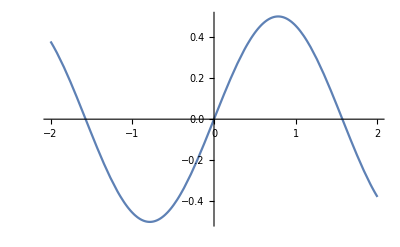

```mathematica
p1 = Plot[f[x], {x, -2, 2}]
```

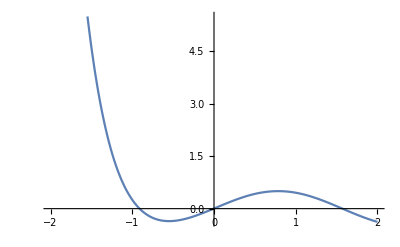

```mathematica
p2 = Plot[g[x], {x, -2, 2}]
```

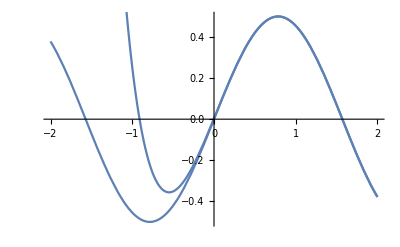

```mathematica
Show[p1, p2]
```

```mathematica
g[.25]
```

0.240237

```mathematica
f[.25]
```

0.239713

Problem 6

```mathematica
ClearAll
```

ClearAll

```mathematica
f[θ_] = 6Cos[θ];
```

```mathematica
g[θ_] = 2(1 + Cos[θ]);
```

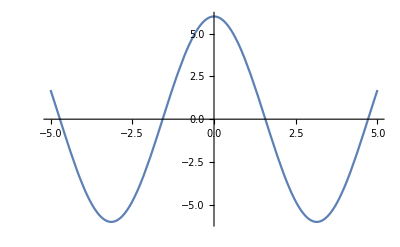

```mathematica
p1 = Plot[f[θ], {θ, -5, 5}]
```

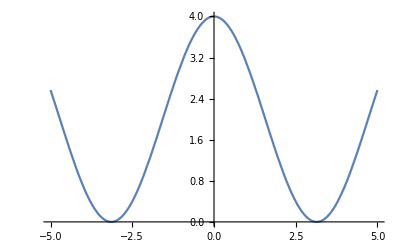

```mathematica
p2 = Plot[g[θ], {θ, -5, 5}]
```

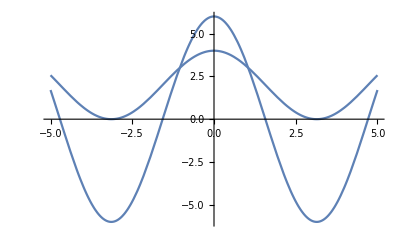

```mathematica
Show[p1, p2]
```

```mathematica
Solve[ 6Cos[θ] == 2(1 + Cos[θ])]
```

{{θ→ConditionalExpression[-π/3+2 π C[1], C[1]∈ℤ]},{θ→ConditionalExpression[π/3+2 π C[1], C[1]∈ℤ]}}

```mathematica
A = 2((1/2)∫_(π/3)^(π/2) ((f[θ])^2 - (g[θ])^2)ⅆθ)
```

2 (-4+π)

Problem 4

```mathematica
ClearAll
```

ClearAll

```mathematica
x[t_] = Log[E, (Sec[t] + Tan[t])] - Sin[t];
```

```mathematica
y[t_] = Cos[t];
```

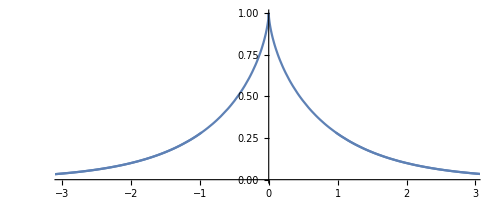

```mathematica
p1 = ParametricPlot[{x[t],y[t]},{t,-5,5}]
```

```mathematica
x'[t]
```

-Cos[t]+(Sec[t]^2+Sec[t] Tan[t])/(Sec[t]+Tan[t])

```mathematica
y'[t]
```

-Sin[t]

```mathematica
S = 2π*∫_0^(Pi/3) ((Cos[t])*√((x'[t])^2 + (y'[t])^2))ⅆt
```

π